# Análisis de grafos para los partidos de Argentina en el mundial FIFA 2014

## Inicialización y carga de datos

```mathematica
SetDirectory[NotebookDirectory[]];
files = FileNames["*Argentina.txt",{"./fifa_2014_pass_distributions/mathematica_data/networks/"}];
```

## Análisis para grafos dirigidos

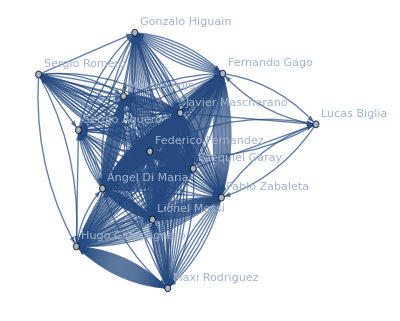
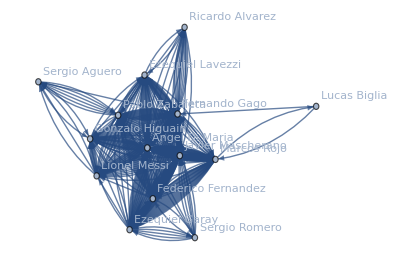
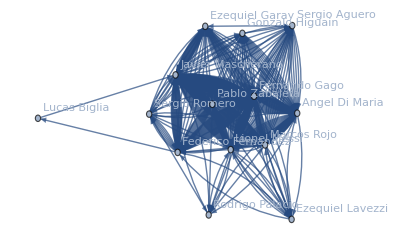
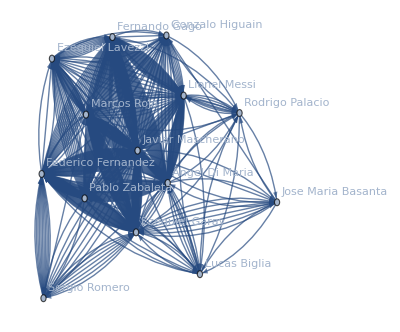
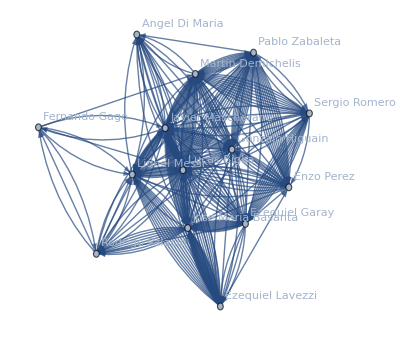
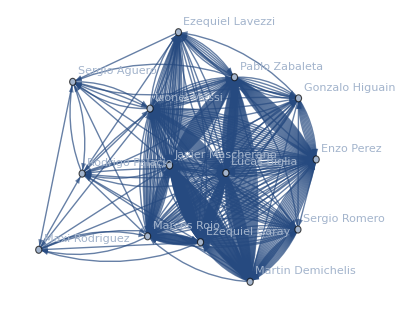
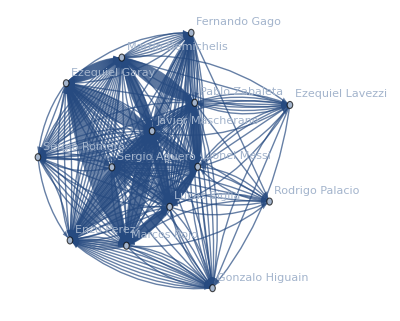

```mathematica
data=ToExpression[Import[#]&/@files];
graphs = Graph[#, VertexLabels->"Name"]&/@data
```

### Grafo resaltado jerárquicamente por el grado de los vértices

```mathematica
HighlightGraph[#,VertexList[#],VertexSize->Thread[VertexList[#]->Rescale[DegreeCentrality[#]]]]&/@graphs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Cada red community plot

```mathematica
Table[CommunityGraphPlot[graphs[[i]]],{i,1,Length[graphs]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Análisis para grafos no dirigidos

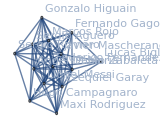
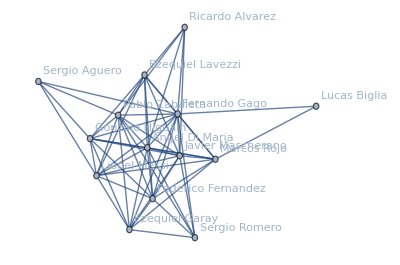
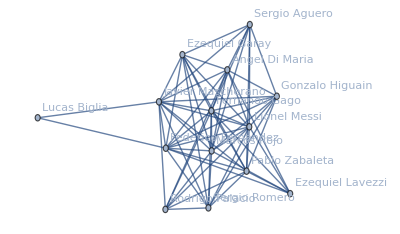
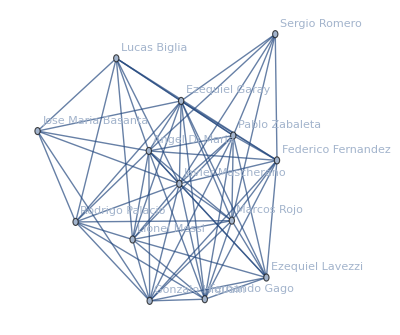
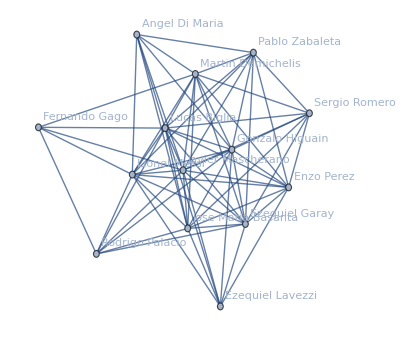
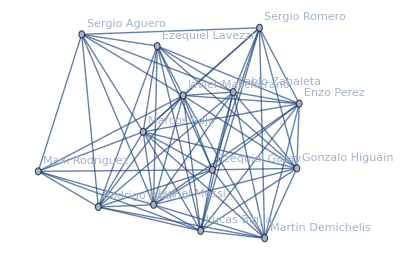
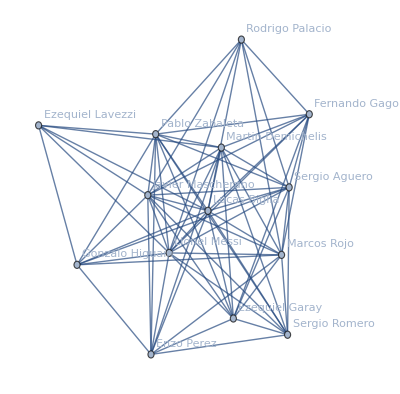

```mathematica
undirectedGraphs = UndirectedGraph[Graph[#], VertexLabels->"Name"]&/@data
```

### Histrograma agregado para la distribuciíon del grado de las redes

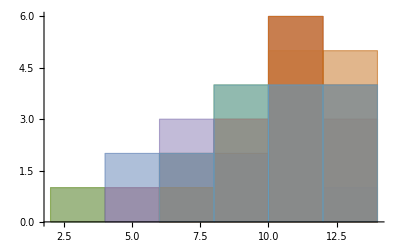

```mathematica
Histogram[DegreeCentrality[#]&/@undirectedGraphs]
```

### Histograma para cada la distribución del grado de cada una de las redes

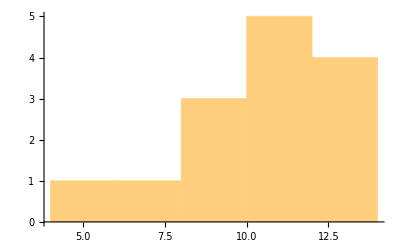
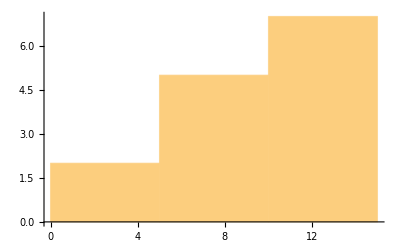
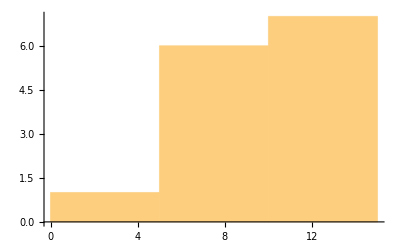
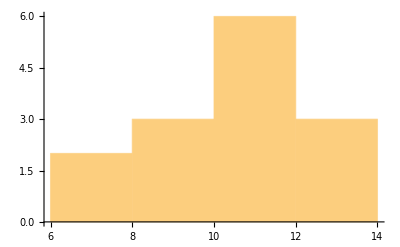
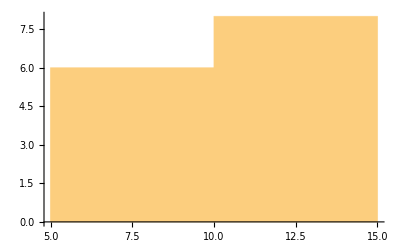
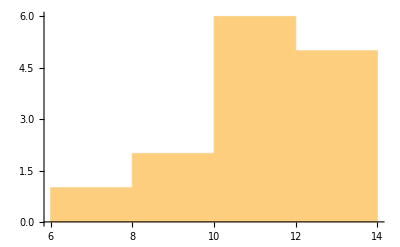
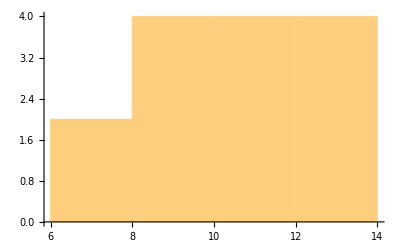

```mathematica
Table[Histogram[DegreeCentrality[undirectedGraphs[[i]]]], {i, 1, Length[undirectedGraphs]}]
```

### Media del grado para cada una de las redes

{71/7,60/7,64/7,69/7,68/7,73/7,71/7}

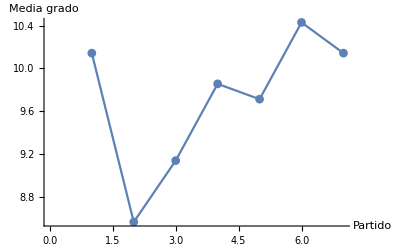

```mathematica
mediagradoUn=Table[Mean[VertexDegree[undirectedGraphs[[i]]]], {i, 1, Length[undirectedGraphs]}]
ejeX={1,2,3,4,5,6,7};
ListPlot[Table[{ejeX[[i]],mediagradoUn[[i]]},{i,1,Length[graphs]}],AxesLabel->{"Partido","Media grado"},Joined->True,PlotMarkers->Automatic]
```

### Media Path Lenght para cada una de las redes

```mathematica
mediaavplUn=Table[N[Mean[Flatten[GraphDistanceMatrix[undirectedGraphs[[i]]]]]],{i,1,Length[undirectedGraphs]}]
```

{1.13265,1.2449,1.20408,1.15306,1.16327,1.11224,1.13265}

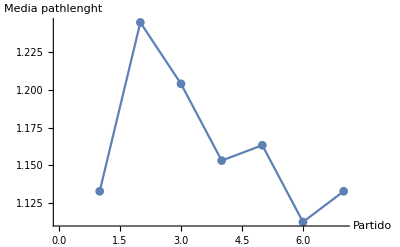

```mathematica
ListPlot[Table[{ejeX[[i]],mediaavplUn[[i]]},{i,1,Length[graphs]}],AxesLabel->{"Partido","Media pathlenght"},Joined->True,PlotMarkers->Automatic]
```

### Clustering coefficient para cada una de las redes

```mathematica
clusteringCoefficients = N[GlobalClusteringCoefficient[#]&/@undirectedGraphs]
```

{0.824561,0.787645,0.772329,0.794393,0.798425,0.818953,0.809384}

## Calculando Small World Coefficient para cada grafo usando la definición de Humphries et. al. 2006 Para esta medida particular se cumple que todo valor superior a 1 hace de la red analizada una red con características Small World.

```mathematica
ramdonEquivalent[input_] := RandomGraph[{VertexCount[input], EdgeCount[input]}]
randomGraphs = ramdonEquivalent[#]&/@undirectedGraphs;
```

```mathematica
smallWorldCoefficient[graph_, equivalentRamdon_]:= (GlobalClusteringCoefficient[graph]/GlobalClusteringCoefficient[equivalentRamdon])/(Mean[Flatten[GraphDistanceMatrix[graph]]]/ Mean[Flatten[GraphDistanceMatrix[equivalentRamdon]]]);

N[Table[smallWorldCoefficient[undirectedGraphs[[i]], randomGraphs[[i]]], {i, 1, Length[undirectedGraphs]}]]
```

{1.08617,1.16908,1.06293,1.03945,1.07521,1.03824,1.05364}

## Calculando Small World Measure para cada grafo usando la definición de Joyce et. al. 2011 Para esta medida particular se cumple que todo valor cercano a 0 hace de la red analizada una red con características Small World. Los valores positivos cercanos a 0 caracterizan redes con más similitud a redes aletorias, las redes con valores negativos cercanos a 0 caracterizan redes con más similitud a redes lattice.

```mathematica
lattice[L_List,r_: 1]:=With[{d=Length[L],LL=Reverse@FoldList[Times,1,Reverse@Abs@L][[1;;-2]]},With[{δ=Pick[#,UnitStep[#-1] UnitStep[r^2-#]&@Total[#^2,{2}],1]&@Tuples[Range[-#,#]&@Ceiling[r],d]},Module[{Id=Join@@Table[Transpose[{#,#+δ[[i]]},{2,3,1}],{i,Length[δ]}]&@Transpose@Tuples[Range/@Abs[L]]-1},Do[If[L[[i]]>0,Id=Pick[Id,UnitStep[#] UnitStep[L[[i]]-1-#]&@Id[[All,2,i]],1],Id[[All,All,i]]=Mod[Id[[All,All,i]],-L[[i]]]],{i,d}];
SparseArray[1+Id.LL->ConstantArray[1,Length[Id]]]]]];
equivalentLattices= AdjacencyGraph@lattice[{VertexCount[#]}, Mean[VertexDegree[#]]] &/@undirectedGraphs
```

```mathematica
smallWorldMeasure[graph_,equivalentRamdon_, equivalentLattice_]:= ( Mean[Flatten[GraphDistanceMatrix[equivalentRamdon]]]/Mean[Flatten[GraphDistanceMatrix[graph]]]) -(GlobalClusteringCoefficient[graph]/GlobalClusteringCoefficient[equivalentLattice]);
```

```mathematica
N[Table[smallWorldMeasure[undirectedGraphs[[i]], randomGraphs[[i]],equivalentLattices[[i]] ], {i, 1, Length[undirectedGraphs]}]]
```

{0.124133,0.0951462,0.149658,0.125366,0.120926,0.13009,0.140254}